## Importing Libraries

```mathematica
PacletDirectoryAdd[NotebookDirectory[]];
```

```mathematica
$ContextPath
```

{XMPTools`,JLink`,WolframAlphaClient`,StreamingLoader`,InterpreterLoader`,IconizeLoader`,HTTPHandlingLoader`,CloudObjectLoader`,PacletManager`,System`,Global`}

```mathematica
<<ResistorProject`
```

prepareImage::shdw: Symbol prepareImage appears in multiple contexts {ResistorProject`,Global`}; definitions in context ResistorProject` may shadow or be shadowed by other definitions.

## Import images

```mathematica
imagesPath = NotebookDirectory[] <> "ResistorProject/Assets/Images/";
dataPath = NotebookDirectory[] <> "ResistorProject/Assets/Data/";
```

```mathematica
importByType [type_String] :=
	Map[
		Import,
		FileNames["*.jpg", imagesPath <> type <> "/"]
	];
```

```mathematica
cutSampleResistor[image_] := Module[
	{comp, div, centers, recPos, dim, img},
	dim = ImageDimensions[image];
	If[dim[[1]] > dim[[2]],
		img = ImageRotate[image],
		img = image
	];
	comp = MorphologicalComponents[
		DeleteSmallComponents[
			ColorNegate @ Binarize[
				ColorConvert[img,"Grayscale"] ^(1/5.2)
			]
		]
	];
	recPos = Values[ComponentMeasurements[comp, "MinimalBoundingBox"]];
	div = Map[Mean,Partition[Sort @ Flatten[recPos[[All, All, 2]]],2]];
	div = Take[div, {2, -2}];
	centers = Table[Mean[{div[[x]], div[[x+1]]}], {x, 1, Length[div] - 1, 2}];
	centers = Flatten[{1, centers, -1}];
		Table[
			ImageTake[img, {-centers[[x+1]], -centers[[x]]}, {1, -1}],
			{x, 1, Length[centers] - 1}
		]
]
```

```mathematica
equalizeSize[image_] := Module[
{width, height, img},
	width = 1400;
	height = 350;
	img = ImageResize[image, {Automatic, height}];
	img = ImageCrop[img, {width, height}, Padding->"Fixed"]
]
```

```mathematica
(*types = {"220KOhm", "4.7KOhm", "10Ohm"};
catImages = Flatten @ Map[ 
	ReplaceAll[importByType[#], x_Image:>{x->#}]&,
	types
];*)

produceData[types_] := 
	Flatten @ Table[
		Module[
			{pictures},
			pictures = importByType[types[[x]]];
			pictures = Flatten[Map[cutSampleResistor,pictures]];
			pictures = Map[RemoveAlphaChannel[prepareImage[equalizeSize[#]]]&, pictures];
			pictures = ReplaceAll[pictures, a_Image:>(a->types[[x]])]
		],
		{x, 1, Length[types]}
	]
```

```mathematica
Map[dataPath<>#&,FileNames[]]
```

{/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.anaconda,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/anaconda,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.android,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/AndroidStudioProjects,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/Applications,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.atom,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.bash_history,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.bash_profile,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.bash_profile-anaconda.bak,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.bash_profile.macports-saved_2016-10-24_at_16:07:36,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.bash_sessions,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.cache,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.CFUserTextEncoding,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.conda,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.config,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.continuum,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/Desktop,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/Documents,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/Downloads,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.DS_Store,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.emulator_console_auth_token,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.gdbinit,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.gitconfig,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.gradle,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/Library,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.lldb,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.local,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/macports,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.matplotlib,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/Maxwell,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/Movies,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/Music,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/NetBeansProjects,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/New Unity Project,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/opencv,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/opencv_contrib,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.oracle_jre_usage,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/Pictures,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/Proyecto,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/Public,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.pylint.d,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.python_history,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.sh_history,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.subversion,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.thumbnails,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.Trash,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.viminfo,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/VirtualBox VMs,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.virtualenvs,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/.wapi}

```mathematica
SetDirectory[dataPath];
types = Select[Map[dataPath<>#&,FileNames[]],DirectoryQ];
Print[types];
Print[FileNames[]];
```

{/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/10Ohm,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/220KOhm,/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/Data/4.7KOhm}

{10Ohm,220KOhm,4.7KOhm,.DS_Store}

```mathematica
SetDirectory[dataPath];
types = Select[Map[dataPath <> #&,FileNames[]],DirectoryQ];
If [Length[types] == 0,
	Module[
		{imageNumber, path},
		SetDirectory[imagesPath];
		imageNumber = 0;
		types = FileNames[];
		data = produceData[types];
		KeyValueMap[
			Module[
				{folderPath},
				folderPath = dataPath <> #2 <> "/";
				If[!DirectoryQ[folderPath], CreateDirectory[folderPath]];
				Export[folderPath <> "/data" <> ToString[imageNumber++] <> ".png", #1]
			]&,
			Association[data]
		]
	],
	types = Map[StringDrop[#,StringLength[dataPath]]&, types];
	f[type_] := Map[
		Import[#]->type&,
		Join[FileNames["*.png", dataPath <> type <> "/"], FileNames["*.jpg", dataPath <> type <> "/"]]
	];
	data = Flatten @ Map[
		f,
		types
	]
];
ResetDirectory[];
```

## Process

```mathematica
data
```

```mathematica
Length[data]
```

85

```mathematica
dataset = RandomSample[data];
```

```mathematica
trainingset = dataset[[;;60]];
testset=dataset[[61;;]];
c = Classify[trainingset, FeatureExtractor->"PixelVector",
Method->"NeuralNetwork",
PerformanceGoal->"Quality"
]
```

ClassifierFunction[…]

```mathematica
cm = ClassifierMeasurements[c,testset];
```

```mathematica
cm["Accuracy"]
```

0.72

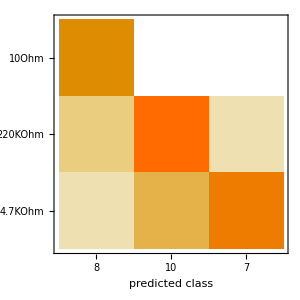

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
c[-Graphics-,"Probabilities"]
```

<|10Ohm→0.369277,220KOhm→0.0134079,4.7KOhm→0.617315|>